```mathematica
Clear[α,ω,p]
```

```mathematica
r=(√(1+(8 ct)/α) (1+(1+1/p)(α/4(√(1+(8 ct)/α)-1))^2 +ω/p(α/4(√(1+(8 ct)/α)-1))^4)^2)/(α/2(√(1+(8 ct)/α)-1) (1-ω/p(α/4(√(1+(8 ct)/α)-1))^4));
```

```mathematica
s=(α/2(√(1+(8 ct)/α)-1) (1-ω/p(α/4(√(1+(8 ct)/α)-1))^4)ct)/(√(1+(8 ct)/α) (1+(1+1/p)(α/4(√(1+(8 ct)/α)-1))^2 +ω/p(α/4(√(1+(8 ct)/α)-1))^4)^2)-(α/4(√(1+(8 ct)/α)-1))^2/(1+(1+1/p)(α/4(√(1+(8 ct)/α)-1))^2 +ω/p(α/4(√(1+(8 ct)/α)-1))^4);
```

EcoRV :

```mathematica
α=4.2
ω=1.
p=5.
```

4.2

1.

5.

```mathematica
cc=Table[{r,s,ct},{ct,0.001,0.86,0.001}]
```

{{500.715,9.98095×10^-7,0.001},{250.716,3.98476×10^-6,0.002},{167.384,8.94856×10^-6,0.003},{125.719,0.000015878,0.004},{100.72,0.0000247618,0.005},{84.0542,0.0000355883,0.006},{72.1505,0.0000483462,0.007},{63.223,0.000063024,0.008},{56.2797,0.0000796103,0.009},{50.7252,0.0000980936,0.01},{46.1809,0.000118462,0.011},{42.3941,0.000140705,0.012},{39.1901,0.000164811,0.013},{36.4439,0.000190767,0.014},{34.0641,0.000218564,0.015},{31.9818,0.000248188,0.016},{30.1447,0.00027963,0.017},{28.5118,0.000312876,0.018},{27.051,0.000347917,0.019},{25.7363,0.00038474,0.02},{24.5469,0.000423334,0.021},{23.4658,0.000463687,0.022},{22.4788,0.000505789,0.023},{21.5741,0.000549627,0.024},{20.7419,0.00059519,0.025},{19.9738,0.000642467,0.026},{19.2626,0.000691447,0.027},{18.6024,0.000742117,0.028},{17.9878,0.000794466,0.029},{17.4142,0.000848484,0.03},{16.8777,0.000904159,0.031},{16.3748,0.000961478,0.032},{15.9024,0.00102043,0.033},{15.4579,0.00108101,0.034},{15.0389,0.00114319,0.035},{14.6432,0.00120698,0.036},{14.269,0.00127235,0.037},{13.9145,0.00133931,0.038},{13.5782,0.00140782,0.039},{13.2589,0.00147789,0.04},{12.9551,0.00154951,0.041},{12.6659,0.00162265,0.042},{12.3902,0.00169732,0.043},{12.1271,0.00177349,0.044},{11.8757,0.00185117,0.045},{11.6353,0.00193033,0.046},{11.4052,0.00201096,0.047},{11.1847,0.00209306,0.048},{10.9733,0.00217661,0.049},{10.7704,0.0022616,0.05},{10.5754,0.00234802,0.051},{10.3881,0.00243586,0.052},{10.2078,0.0025251,0.053},{10.0343,0.00261575,0.054},{9.86707,0.00270777,0.055},{9.7059,0.00280118,0.056},{9.55043,0.00289594,0.057},{9.40036,0.00299206,0.058},{9.25541,0.00308951,0.059},{9.11534,0.0031883,0.06},{8.9799,0.00328841,0.061},{8.84887,0.00338982,0.062},{8.72204,0.00349252,0.063},{8.59921,0.00359652,0.064},{8.4802,0.00370178,0.065},{8.36483,0.00380831,0.066},{8.25294,0.00391609,0.067},{8.14437,0.00402511,0.068},{8.039,0.00413537,0.069},{7.93666,0.00424684,0.07},{7.83725,0.00435951,0.071},{7.74063,0.00447339,0.072},{7.64669,0.00458845,0.073},{7.55532,0.00470469,0.074},{7.46643,0.00482209,0.075},{7.3799,0.00494064,0.076},{7.29566,0.00506034,0.077},{7.21361,0.00518117,0.078},{7.13367,0.00530312,0.079},{7.05575,0.00542618,0.08},{6.9798,0.00555033,0.081},{6.90572,0.00567558,0.082},{6.83347,0.00580191,0.083},{6.76296,0.0059293,0.084},{6.69414,0.00605775,0.085},{6.62695,0.00618724,0.086},{6.56134,0.00631777,0.087},{6.49724,0.00644932,0.088},{6.43462,0.00658189,0.089},{6.37341,0.00671546,0.09},{6.31358,0.00685002,0.091},{6.25508,0.00698557,0.092},{6.19786,0.00712209,0.093},{6.14189,0.00725956,0.094},{6.08713,0.00739799,0.095},{6.03353,0.00753736,0.096},{5.98106,0.00767766,0.097},{5.9297,0.00781887,0.098},{5.87939,0.007961,0.099},{5.83012,0.00810402,0.1},{5.78185,0.00824794,0.101},{5.73455,0.00839273,0.102},{5.6882,0.00853838,0.103},{5.64276,0.0086849,0.104},{5.59821,0.00883226,0.105},{5.55453,0.00898046,0.106},{5.51169,0.00912948,0.107},{5.46967,0.00927933,0.108},{5.42845,0.00942997,0.109},{5.388,0.00958142,0.11},{5.3483,0.00973364,0.111},{5.30933,0.00988665,0.112},{5.27108,0.0100404,0.113},{5.23352,0.0101949,0.114},{5.19664,0.0103502,0.115},{5.16042,0.0105062,0.116},{5.12484,0.010663,0.117},{5.08988,0.0108204,0.118},{5.05554,0.0109786,0.119},{5.02179,0.0111374,0.12},{4.98862,0.011297,0.121},{4.95602,0.0114572,0.122},{4.92397,0.011618,0.123},{4.89246,0.0117796,0.124},{4.86148,0.0119418,0.125},{4.83101,0.0121046,0.126},{4.80104,0.012268,0.127},{4.77156,0.0124321,0.128},{4.74256,0.0125968,0.129},{4.71403,0.0127621,0.13},{4.68595,0.0129279,0.131},{4.65832,0.0130944,0.132},{4.63113,0.0132614,0.133},{4.60437,0.0134289,0.134},{4.57802,0.0135971,0.135},{4.55208,0.0137657,0.136},{4.52654,0.0139349,0.137},{4.50139,0.0141047,0.138},{4.47662,0.0142749,0.139},{4.45222,0.0144456,0.14},{4.42819,0.0146169,0.141},{4.40453,0.0147886,0.142},{4.38121,0.0149608,0.143},{4.35823,0.0151334,0.144},{4.33559,0.0153066,0.145},{4.31329,0.0154801,0.146},{4.2913,0.0156541,0.147},{4.26963,0.0158286,0.148},{4.24827,0.0160034,0.149},{4.22722,0.0161787,0.15},{4.20646,0.0163544,0.151},{4.186,0.0165305,0.152},{4.16582,0.0167069,0.153},{4.14592,0.0168838,0.154},{4.1263,0.017061,0.155},{4.10695,0.0172385,0.156},{4.08786,0.0174164,0.157},{4.06904,0.0175947,0.158},{4.05047,0.0177733,0.159},{4.03215,0.0179522,0.16},{4.01408,0.0181314,0.161},{3.99624,0.018311,0.162},{3.97865,0.0184908,0.163},{3.96129,0.0186709,0.164},{3.94415,0.0188513,0.165},{3.92724,0.019032,0.166},{3.91055,0.0192129,0.167},{3.89408,0.0193941,0.168},{3.87782,0.0195755,0.169},{3.86177,0.0197572,0.17},{3.84592,0.0199391,0.171},{3.83028,0.0201213,0.172},{3.81483,0.0203036,0.173},{3.79958,0.0204861,0.174},{3.78452,0.0206689,0.175},{3.76965,0.0208518,0.176},{3.75497,0.0210349,0.177},{3.74046,0.0212182,0.178},{3.72614,0.0214017,0.179},{3.71199,0.0215853,0.18},{3.69802,0.021769,0.181},{3.68421,0.0219529,0.182},{3.67058,0.022137,0.183},{3.65711,0.0223211,0.184},{3.6438,0.0225054,0.185},{3.63065,0.0226897,0.186},{3.61766,0.0228742,0.187},{3.60482,0.0230588,0.188},{3.59213,0.0232434,0.189},{3.5796,0.0234282,0.19},{3.56721,0.023613,0.191},{3.55497,0.0237978,0.192},{3.54287,0.0239827,0.193},{3.53091,0.0241677,0.194},{3.5191,0.0243527,0.195},{3.50741,0.0245377,0.196},{3.49587,0.0247228,0.197},{3.48445,0.0249078,0.198},{3.47317,0.0250929,0.199},{3.46201,0.025278,0.2},{3.45099,0.0254631,0.201},{3.44008,0.0256481,0.202},{3.4293,0.0258332,0.203},{3.41864,0.0260182,0.204},{3.40811,0.0262032,0.205},{3.39769,0.0263881,0.206},{3.38738,0.026573,0.207},{3.37719,0.0267578,0.208},{3.36711,0.0269425,0.209},{3.35715,0.0271272,0.21},{3.34729,0.0273118,0.211},{3.33755,0.0274964,0.212},{3.32791,0.0276808,0.213},{3.31837,0.0278651,0.214},{3.30894,0.0280493,0.215},{3.29961,0.0282335,0.216},{3.29039,0.0284175,0.217},{3.28126,0.0286013,0.218},{3.27223,0.028785,0.219},{3.2633,0.0289686,0.22},{3.25447,0.0291521,0.221},{3.24573,0.0293354,0.222},{3.23708,0.0295185,0.223},{3.22852,0.0297014,0.224},{3.22006,0.0298842,0.225},{3.21168,0.0300668,0.226},{3.2034,0.0302492,0.227},{3.1952,0.0304315,0.228},{3.18709,0.0306135,0.229},{3.17906,0.0307953,0.23},{3.17112,0.0309769,0.231},{3.16326,0.0311583,0.232},{3.15548,0.0313394,0.233},{3.14779,0.0315204,0.234},{3.14017,0.031701,0.235},{3.13263,0.0318815,0.236},{3.12517,0.0320617,0.237},{3.11779,0.0322416,0.238},{3.11049,0.0324213,0.239},{3.10326,0.0326007,0.24},{3.0961,0.0327798,0.241},{3.08902,0.0329586,0.242},{3.08201,0.0331372,0.243},{3.07507,0.0333155,0.244},{3.0682,0.0334934,0.245},{3.0614,0.0336711,0.246},{3.05468,0.0338484,0.247},{3.04802,0.0340254,0.248},{3.04142,0.0342021,0.249},{3.0349,0.0343785,0.25},{3.02844,0.0345546,0.251},{3.02205,0.0347303,0.252},{3.01572,0.0349056,0.253},{3.00945,0.0350806,0.254},{3.00325,0.0352553,0.255},{2.99711,0.0354295,0.256},{2.99103,0.0356035,0.257},{2.98501,0.035777,0.258},{2.97906,0.0359502,0.259},{2.97316,0.0361229,0.26},{2.96732,0.0362953,0.261},{2.96154,0.0364673,0.262},{2.95582,0.0366389,0.263},{2.95016,0.0368101,0.264},{2.94455,0.0369808,0.265},{2.93899,0.0371512,0.266},{2.9335,0.0373211,0.267},{2.92805,0.0374906,0.268},{2.92267,0.0376597,0.269},{2.91733,0.0378283,0.27},{2.91205,0.0379965,0.271},{2.90682,0.0381642,0.272},{2.90164,0.0383315,0.273},{2.89651,0.0384984,0.274},{2.89144,0.0386647,0.275},{2.88641,0.0388306,0.276},{2.88144,0.038996,0.277},{2.87651,0.039161,0.278},{2.87163,0.0393254,0.279},{2.8668,0.0394894,0.28},{2.86202,0.0396529,0.281},{2.85729,0.0398159,0.282},{2.8526,0.0399784,0.283},{2.84796,0.0401403,0.284},{2.84336,0.0403018,0.285},{2.83881,0.0404627,0.286},{2.83431,0.0406232,0.287},{2.82984,0.0407831,0.288},{2.82543,0.0409424,0.289},{2.82105,0.0411013,0.29},{2.81672,0.0412596,0.291},{2.81244,0.0414173,0.292},{2.80819,0.0415745,0.293},{2.80399,0.0417312,0.294},{2.79983,0.0418873,0.295},{2.79571,0.0420428,0.296},{2.79163,0.0421978,0.297},{2.78759,0.0423522,0.298},{2.78359,0.042506,0.299},{2.77963,0.0426593,0.3},{2.77571,0.0428119,0.301},{2.77183,0.042964,0.302},{2.76799,0.0431155,0.303},{2.76419,0.0432664,0.304},{2.76042,0.0434167,0.305},{2.75669,0.0435664,0.306},{2.753,0.0437155,0.307},{2.74935,0.0438639,0.308},{2.74573,0.0440118,0.309},{2.74214,0.0441591,0.31},{2.7386,0.0443057,0.311},{2.73509,0.0444517,0.312},{2.73161,0.044597,0.313},{2.72817,0.0447418,0.314},{2.72477,0.0448859,0.315},{2.7214,0.0450293,0.316},{2.71806,0.0451721,0.317},{2.71475,0.0453143,0.318},{2.71148,0.0454558,0.319},{2.70825,0.0455966,0.32},{2.70504,0.0457368,0.321},{2.70187,0.0458763,0.322},{2.69873,0.0460152,0.323},{2.69562,0.0461534,0.324},{2.69255,0.0462909,0.325},{2.6895,0.0464277,0.326},{2.68649,0.0465639,0.327},{2.68351,0.0466993,0.328},{2.68056,0.0468341,0.329},{2.67764,0.0469682,0.33},{2.67475,0.0471016,0.331},{2.67188,0.0472343,0.332},{2.66905,0.0473663,0.333},{2.66625,0.0474976,0.334},{2.66348,0.0476281,0.335},{2.66074,0.047758,0.336},{2.65802,0.0478872,0.337},{2.65534,0.0480156,0.338},{2.65268,0.0481433,0.339},{2.65005,0.0482703,0.34},{2.64745,0.0483966,0.341},{2.64487,0.0485222,0.342},{2.64233,0.048647,0.343},{2.63981,0.048771,0.344},{2.63731,0.0488944,0.345},{2.63485,0.049017,0.346},{2.63241,0.0491388,0.347},{2.63,0.0492599,0.348},{2.62761,0.0493803,0.349},{2.62525,0.0494999,0.35},{2.62291,0.0496187,0.351},{2.6206,0.0497368,0.352},{2.61832,0.0498542,0.353},{2.61606,0.0499707,0.354},{2.61383,0.0500865,0.355},{2.61162,0.0502015,0.356},{2.60944,0.0503158,0.357},{2.60728,0.0504293,0.358},{2.60514,0.050542,0.359},{2.60303,0.0506539,0.36},{2.60094,0.0507651,0.361},{2.59888,0.0508754,0.362},{2.59684,0.050985,0.363},{2.59482,0.0510938,0.364},{2.59283,0.0512018,0.365},{2.59086,0.051309,0.366},{2.58891,0.0514154,0.367},{2.58699,0.051521,0.368},{2.58508,0.0516258,0.369},{2.5832,0.0517298,0.37},{2.58135,0.051833,0.371},{2.57951,0.0519354,0.372},{2.5777,0.052037,0.373},{2.57591,0.0521377,0.374},{2.57414,0.0522377,0.375},{2.57239,0.0523368,0.376},{2.57066,0.0524351,0.377},{2.56896,0.0525326,0.378},{2.56727,0.0526293,0.379},{2.56561,0.0527251,0.38},{2.56397,0.0528201,0.381},{2.56235,0.0529143,0.382},{2.56074,0.0530077,0.383},{2.55916,0.0531002,0.384},{2.5576,0.0531919,0.385},{2.55606,0.0532827,0.386},{2.55454,0.0533727,0.387},{2.55304,0.0534619,0.388},{2.55156,0.0535502,0.389},{2.5501,0.0536377,0.39},{2.54866,0.0537244,0.391},{2.54723,0.0538101,0.392},{2.54583,0.0538951,0.393},{2.54445,0.0539792,0.394},{2.54308,0.0540624,0.395},{2.54173,0.0541448,0.396},{2.54041,0.0542263,0.397},{2.5391,0.054307,0.398},{2.53781,0.0543868,0.399},{2.53653,0.0544657,0.4},{2.53528,0.0545438,0.401},{2.53405,0.054621,0.402},{2.53283,0.0546973,0.403},{2.53163,0.0547728,0.404},{2.53045,0.0548474,0.405},{2.52928,0.0549212,0.406},{2.52814,0.054994,0.407},{2.52701,0.055066,0.408},{2.5259,0.0551371,0.409},{2.5248,0.0552074,0.41},{2.52373,0.0552767,0.411},{2.52267,0.0553452,0.412},{2.52162,0.0554128,0.413},{2.5206,0.0554795,0.414},{2.51959,0.0555454,0.415},{2.5186,0.0556103,0.416},{2.51762,0.0556744,0.417},{2.51666,0.0557376,0.418},{2.51572,0.0557999,0.419},{2.5148,0.0558613,0.42},{2.51389,0.0559218,0.421},{2.51299,0.0559814,0.422},{2.51212,0.0560401,0.423},{2.51125,0.056098,0.424},{2.51041,0.0561549,0.425},{2.50958,0.0562109,0.426},{2.50876,0.0562661,0.427},{2.50797,0.0563203,0.428},{2.50718,0.0563737,0.429},{2.50642,0.0564261,0.43},{2.50566,0.0564777,0.431},{2.50493,0.0565283,0.432},{2.50421,0.0565781,0.433},{2.5035,0.0566269,0.434},{2.50281,0.0566748,0.435},{2.50213,0.0567218,0.436},{2.50147,0.056768,0.437},{2.50082,0.0568132,0.438},{2.50019,0.0568575,0.439},{2.49958,0.0569009,0.44},{2.49897,0.0569434,0.441},{2.49839,0.0569849,0.442},{2.49781,0.0570256,0.443},{2.49725,0.0570653,0.444},{2.49671,0.0571042,0.445},{2.49618,0.0571421,0.446},{2.49566,0.0571791,0.447},{2.49516,0.0572152,0.448},{2.49467,0.0572504,0.449},{2.4942,0.0572846,0.45},{2.49374,0.057318,0.451},{2.49329,0.0573504,0.452},{2.49286,0.0573819,0.453},{2.49244,0.0574125,0.454},{2.49203,0.0574422,0.455},{2.49164,0.0574709,0.456},{2.49126,0.0574988,0.457},{2.4909,0.0575257,0.458},{2.49054,0.0575517,0.459},{2.49021,0.0575767,0.46},{2.48988,0.0576009,0.461},{2.48957,0.0576241,0.462},{2.48927,0.0576464,0.463},{2.48898,0.0576678,0.464},{2.48871,0.0576882,0.465},{2.48845,0.0577078,0.466},{2.48821,0.0577264,0.467},{2.48797,0.0577441,0.468},{2.48775,0.0577608,0.469},{2.48754,0.0577767,0.47},{2.48734,0.0577916,0.471},{2.48716,0.0578056,0.472},{2.48699,0.0578186,0.473},{2.48683,0.0578307,0.474},{2.48669,0.0578419,0.475},{2.48655,0.0578522,0.476},{2.48643,0.0578616,0.477},{2.48632,0.05787,0.478},{2.48623,0.0578775,0.479},{2.48614,0.0578841,0.48},{2.48607,0.0578897,0.481},{2.48601,0.0578944,0.482},{2.48596,0.0578982,0.483},{2.48592,0.0579011,0.484},{2.4859,0.057903,0.485},{2.48588,0.057904,0.486},{2.48588,0.0579041,0.487},{2.48589,0.0579032,0.488},{2.48592,0.0579014,0.489},{2.48595,0.0578987,0.49},{2.486,0.0578951,0.491},{2.48605,0.0578905,0.492},{2.48612,0.057885,0.493},{2.4862,0.0578786,0.494},{2.4863,0.0578713,0.495},{2.4864,0.057863,0.496},{2.48651,0.0578538,0.497},{2.48664,0.0578437,0.498},{2.48678,0.0578326,0.499},{2.48692,0.0578207,0.5},{2.48708,0.0578077,0.501},{2.48725,0.0577939,0.502},{2.48744,0.0577791,0.503},{2.48763,0.0577635,0.504},{2.48783,0.0577468,0.505},{2.48805,0.0577293,0.506},{2.48827,0.0577108,0.507},{2.48851,0.0576915,0.508},{2.48876,0.0576711,0.509},{2.48902,0.0576499,0.51},{2.48928,0.0576277,0.511},{2.48956,0.0576047,0.512},{2.48985,0.0575806,0.513},{2.49016,0.0575557,0.514},{2.49047,0.0575298,0.515},{2.49079,0.0575031,0.516},{2.49112,0.0574754,0.517},{2.49147,0.0574467,0.518},{2.49182,0.0574172,0.519},{2.49218,0.0573867,0.52},{2.49256,0.0573553,0.521},{2.49294,0.057323,0.522},{2.49334,0.0572898,0.523},{2.49374,0.0572556,0.524},{2.49416,0.0572206,0.525},{2.49459,0.0571846,0.526},{2.49502,0.0571477,0.527},{2.49547,0.0571099,0.528},{2.49593,0.0570711,0.529},{2.49639,0.0570315,0.53},{2.49687,0.0569909,0.531},{2.49736,0.0569494,0.532},{2.49785,0.056907,0.533},{2.49836,0.0568637,0.534},{2.49888,0.0568195,0.535},{2.4994,0.0567743,0.536},{2.49994,0.0567283,0.537},{2.50048,0.0566813,0.538},{2.50104,0.0566334,0.539},{2.50161,0.0565846,0.54},{2.50218,0.0565349,0.541},{2.50277,0.0564843,0.542},{2.50336,0.0564328,0.543},{2.50397,0.0563804,0.544},{2.50458,0.056327,0.545},{2.50521,0.0562728,0.546},{2.50584,0.0562176,0.547},{2.50648,0.0561616,0.548},{2.50713,0.0561046,0.549},{2.5078,0.0560468,0.55},{2.50847,0.055988,0.551},{2.50915,0.0559283,0.552},{2.50984,0.0558677,0.553},{2.51054,0.0558063,0.554},{2.51125,0.0557439,0.555},{2.51197,0.0556806,0.556},{2.51269,0.0556165,0.557},{2.51343,0.0555514,0.558},{2.51418,0.0554854,0.559},{2.51493,0.0554186,0.56},{2.5157,0.0553508,0.561},{2.51647,0.0552822,0.562},{2.51726,0.0552126,0.563},{2.51805,0.0551422,0.564},{2.51885,0.0550708,0.565},{2.51966,0.0549986,0.566},{2.52048,0.0549255,0.567},{2.52131,0.0548515,0.568},{2.52215,0.0547766,0.569},{2.52299,0.0547008,0.57},{2.52385,0.0546242,0.571},{2.52471,0.0545466,0.572},{2.52559,0.0544682,0.573},{2.52647,0.0543889,0.574},{2.52736,0.0543087,0.575},{2.52826,0.0542276,0.576},{2.52917,0.0541456,0.577},{2.53009,0.0540628,0.578},{2.53102,0.0539791,0.579},{2.53195,0.0538945,0.58},{2.53289,0.053809,0.581},{2.53385,0.0537226,0.582},{2.53481,0.0536354,0.583},{2.53578,0.0535473,0.584},{2.53676,0.0534583,0.585},{2.53775,0.0533685,0.586},{2.53874,0.0532777,0.587},{2.53975,0.0531862,0.588},{2.54076,0.0530937,0.589},{2.54179,0.0530004,0.59},{2.54282,0.0529062,0.591},{2.54386,0.0528111,0.592},{2.5449,0.0527152,0.593},{2.54596,0.0526184,0.594},{2.54703,0.0525208,0.595},{2.5481,0.0524223,0.596},{2.54918,0.0523229,0.597},{2.55027,0.0522227,0.598},{2.55137,0.0521216,0.599},{2.55248,0.0520196,0.6},{2.55359,0.0519168,0.601},{2.55472,0.0518132,0.602},{2.55585,0.0517087,0.603},{2.55699,0.0516033,0.604},{2.55814,0.0514971,0.605},{2.5593,0.0513901,0.606},{2.56046,0.0512821,0.607},{2.56164,0.0511734,0.608},{2.56282,0.0510638,0.609},{2.56401,0.0509533,0.61},{2.56521,0.0508421,0.611},{2.56642,0.0507299,0.612},{2.56763,0.050617,0.613},{2.56886,0.0505031,0.614},{2.57009,0.0503885,0.615},{2.57133,0.050273,0.616},{2.57258,0.0501567,0.617},{2.57383,0.0500395,0.618},{2.5751,0.0499215,0.619},{2.57637,0.0498027,0.62},{2.57765,0.049683,0.621},{2.57894,0.0495625,0.622},{2.58024,0.0494412,0.623},{2.58154,0.0493191,0.624},{2.58285,0.0491961,0.625},{2.58418,0.0490723,0.626},{2.5855,0.0489477,0.627},{2.58684,0.0488223,0.628},{2.58819,0.048696,0.629},{2.58954,0.0485689,0.63},{2.5909,0.048441,0.631},{2.59227,0.0483123,0.632},{2.59365,0.0481827,0.633},{2.59503,0.0480524,0.634},{2.59642,0.0479212,0.635},{2.59783,0.0477893,0.636},{2.59923,0.0476565,0.637},{2.60065,0.0475229,0.638},{2.60207,0.0473885,0.639},{2.60351,0.0472533,0.64},{2.60495,0.0471173,0.641},{2.6064,0.0469805,0.642},{2.60785,0.0468428,0.643},{2.60931,0.0467044,0.644},{2.61079,0.0465652,0.645},{2.61227,0.0464252,0.646},{2.61375,0.0462844,0.647},{2.61525,0.0461428,0.648},{2.61675,0.0460004,0.649},{2.61826,0.0458572,0.65},{2.61978,0.0457132,0.651},{2.62131,0.0455684,0.652},{2.62284,0.0454228,0.653},{2.62438,0.0452765,0.654},{2.62593,0.0451294,0.655},{2.62749,0.0449814,0.656},{2.62905,0.0448327,0.657},{2.63062,0.0446832,0.658},{2.6322,0.044533,0.659},{2.63379,0.0443819,0.66},{2.63539,0.0442301,0.661},{2.63699,0.0440775,0.662},{2.6386,0.0439242,0.663},{2.64022,0.04377,0.664},{2.64185,0.0436151,0.665},{2.64348,0.0434594,0.666},{2.64512,0.043303,0.667},{2.64677,0.0431458,0.668},{2.64843,0.0429878,0.669},{2.65009,0.0428291,0.67},{2.65176,0.0426696,0.671},{2.65344,0.0425093,0.672},{2.65513,0.0423483,0.673},{2.65682,0.0421865,0.674},{2.65852,0.0420239,0.675},{2.66023,0.0418607,0.676},{2.66195,0.0416966,0.677},{2.66368,0.0415318,0.678},{2.66541,0.0413663,0.679},{2.66715,0.0412,0.68},{2.6689,0.0410329,0.681},{2.67065,0.0408651,0.682},{2.67241,0.0406966,0.683},{2.67418,0.0405273,0.684},{2.67596,0.0403573,0.685},{2.67774,0.0401866,0.686},{2.67954,0.0400151,0.687},{2.68134,0.0398428,0.688},{2.68314,0.0396699,0.689},{2.68496,0.0394962,0.69},{2.68678,0.0393218,0.691},{2.68861,0.0391466,0.692},{2.69045,0.0389707,0.693},{2.69229,0.0387941,0.694},{2.69415,0.0386168,0.695},{2.69601,0.0384387,0.696},{2.69787,0.0382599,0.697},{2.69975,0.0380804,0.698},{2.70163,0.0379002,0.699},{2.70352,0.0377192,0.7},{2.70541,0.0375376,0.701},{2.70732,0.0373552,0.702},{2.70923,0.0371721,0.703},{2.71115,0.0369883,0.704},{2.71308,0.0368038,0.705},{2.71501,0.0366186,0.706},{2.71695,0.0364327,0.707},{2.7189,0.036246,0.708},{2.72086,0.0360587,0.709},{2.72282,0.0358707,0.71},{2.72479,0.0356819,0.711},{2.72677,0.0354925,0.712},{2.72875,0.0353024,0.713},{2.73075,0.0351115,0.714},{2.73275,0.03492,0.715},{2.73475,0.0347278,0.716},{2.73677,0.0345349,0.717},{2.73879,0.0343413,0.718},{2.74082,0.034147,0.719},{2.74286,0.0339521,0.72},{2.7449,0.0337564,0.721},{2.74695,0.0335601,0.722},{2.74901,0.0333631,0.723},{2.75108,0.0331654,0.724},{2.75315,0.032967,0.725},{2.75524,0.0327679,0.726},{2.75732,0.0325682,0.727},{2.75942,0.0323678,0.728},{2.76152,0.0321668,0.729},{2.76363,0.031965,0.73},{2.76575,0.0317626,0.731},{2.76788,0.0315595,0.732},{2.77001,0.0313558,0.733},{2.77215,0.0311514,0.734},{2.7743,0.0309463,0.735},{2.77645,0.0307406,0.736},{2.77861,0.0305342,0.737},{2.78078,0.0303272,0.738},{2.78296,0.0301195,0.739},{2.78514,0.0299111,0.74},{2.78733,0.0297021,0.741},{2.78953,0.0294925,0.742},{2.79174,0.0292822,0.743},{2.79395,0.0290712,0.744},{2.79617,0.0288596,0.745},{2.7984,0.0286474,0.746},{2.80063,0.0284345,0.747},{2.80288,0.028221,0.748},{2.80512,0.0280069,0.749},{2.80738,0.0277921,0.75},{2.80965,0.0275766,0.751},{2.81192,0.0273606,0.752},{2.8142,0.0271439,0.753},{2.81648,0.0269265,0.754},{2.81878,0.0267086,0.755},{2.82108,0.02649,0.756},{2.82338,0.0262708,0.757},{2.8257,0.0260509,0.758},{2.82802,0.0258305,0.759},{2.83035,0.0256094,0.76},{2.83269,0.0253877,0.761},{2.83503,0.0251654,0.762},{2.83739,0.0249424,0.763},{2.83975,0.0247189,0.764},{2.84211,0.0244947,0.765},{2.84449,0.02427,0.766},{2.84687,0.0240446,0.767},{2.84926,0.0238186,0.768},{2.85165,0.023592,0.769},{2.85405,0.0233648,0.77},{2.85646,0.023137,0.771},{2.85888,0.0229086,0.772},{2.86131,0.0226796,0.773},{2.86374,0.02245,0.774},{2.86618,0.0222198,0.775},{2.86863,0.021989,0.776},{2.87108,0.0217576,0.777},{2.87354,0.0215256,0.778},{2.87601,0.021293,0.779},{2.87849,0.0210599,0.78},{2.88097,0.0208261,0.781},{2.88346,0.0205918,0.782},{2.88596,0.0203569,0.783},{2.88846,0.0201214,0.784},{2.89098,0.0198853,0.785},{2.8935,0.0196487,0.786},{2.89603,0.0194115,0.787},{2.89856,0.0191737,0.788},{2.9011,0.0189353,0.789},{2.90365,0.0186963,0.79},{2.90621,0.0184568,0.791},{2.90877,0.0182167,0.792},{2.91134,0.0179761,0.793},{2.91392,0.0177348,0.794},{2.91651,0.0174931,0.795},{2.9191,0.0172507,0.796},{2.9217,0.0170078,0.797},{2.92431,0.0167643,0.798},{2.92693,0.0165203,0.799},{2.92955,0.0162758,0.8},{2.93218,0.0160306,0.801},{2.93482,0.0157849,0.802},{2.93746,0.0155387,0.803},{2.94012,0.0152919,0.804},{2.94278,0.0150446,0.805},{2.94544,0.0147967,0.806},{2.94812,0.0145483,0.807},{2.9508,0.0142993,0.808},{2.95349,0.0140498,0.809},{2.95619,0.0137998,0.81},{2.95889,0.0135492,0.811},{2.9616,0.0132981,0.812},{2.96432,0.0130465,0.813},{2.96705,0.0127943,0.814},{2.96978,0.0125416,0.815},{2.97252,0.0122883,0.816},{2.97527,0.0120345,0.817},{2.97803,0.0117803,0.818},{2.98079,0.0115254,0.819},{2.98356,0.0112701,0.82},{2.98634,0.0110142,0.821},{2.98913,0.0107578,0.822},{2.99192,0.0105009,0.823},{2.99472,0.0102435,0.824},{2.99753,0.00998559,0.825},{3.00035,0.00972715,0.826},{3.00317,0.00946819,0.827},{3.006,0.00920872,0.828},{3.00884,0.00894875,0.829},{3.01168,0.00868827,0.83},{3.01454,0.00842728,0.831},{3.0174,0.00816579,0.832},{3.02027,0.0079038,0.833},{3.02314,0.00764131,0.834},{3.02602,0.00737832,0.835},{3.02891,0.00711483,0.836},{3.03181,0.00685085,0.837},{3.03472,0.00658637,0.838},{3.03763,0.0063214,0.839},{3.04055,0.00605594,0.84},{3.04348,0.00579,0.841},{3.04642,0.00552356,0.842},{3.04936,0.00525664,0.843},{3.05231,0.00498923,0.844},{3.05527,0.00472135,0.845},{3.05823,0.00445298,0.846},{3.06121,0.00418413,0.847},{3.06419,0.0039148,0.848},{3.06718,0.003645,0.849},{3.07017,0.00337473,0.85},{3.07318,0.00310398,0.851},{3.07619,0.00283276,0.852},{3.07921,0.00256107,0.853},{3.08223,0.00228891,0.854},{3.08527,0.00201628,0.855},{3.08831,0.00174319,0.856},{3.09136,0.00146964,0.857},{3.09441,0.00119562,0.858},{3.09748,0.000921146,0.859},{3.10055,0.000646211,0.86}}

```mathematica
ddEcoRV=Table[{cc[[i,1]],cc[[i,2]]},{i,1,860,1}]
```

{{500.715,9.98095×10^-7},{250.716,3.98476×10^-6},{167.384,8.94856×10^-6},{125.719,0.000015878},{100.72,0.0000247618},{84.0542,0.0000355883},{72.1505,0.0000483462},{63.223,0.000063024},{56.2797,0.0000796103},{50.7252,0.0000980936},{46.1809,0.000118462},{42.3941,0.000140705},{39.1901,0.000164811},{36.4439,0.000190767},{34.0641,0.000218564},{31.9818,0.000248188},{30.1447,0.00027963},{28.5118,0.000312876},{27.051,0.000347917},{25.7363,0.00038474},{24.5469,0.000423334},{23.4658,0.000463687},{22.4788,0.000505789},{21.5741,0.000549627},{20.7419,0.00059519},{19.9738,0.000642467},{19.2626,0.000691447},{18.6024,0.000742117},{17.9878,0.000794466},{17.4142,0.000848484},{16.8777,0.000904159},{16.3748,0.000961478},{15.9024,0.00102043},{15.4579,0.00108101},{15.0389,0.00114319},{14.6432,0.00120698},{14.269,0.00127235},{13.9145,0.00133931},{13.5782,0.00140782},{13.2589,0.00147789},{12.9551,0.00154951},{12.6659,0.00162265},{12.3902,0.00169732},{12.1271,0.00177349},{11.8757,0.00185117},{11.6353,0.00193033},{11.4052,0.00201096},{11.1847,0.00209306},{10.9733,0.00217661},{10.7704,0.0022616},{10.5754,0.00234802},{10.3881,0.00243586},{10.2078,0.0025251},{10.0343,0.00261575},{9.86707,0.00270777},{9.7059,0.00280118},{9.55043,0.00289594},{9.40036,0.00299206},{9.25541,0.00308951},{9.11534,0.0031883},{8.9799,0.00328841},{8.84887,0.00338982},{8.72204,0.00349252},{8.59921,0.00359652},{8.4802,0.00370178},{8.36483,0.00380831},{8.25294,0.00391609},{8.14437,0.00402511},{8.039,0.00413537},{7.93666,0.00424684},{7.83725,0.00435951},{7.74063,0.00447339},{7.64669,0.00458845},{7.55532,0.00470469},{7.46643,0.00482209},{7.3799,0.00494064},{7.29566,0.00506034},{7.21361,0.00518117},{7.13367,0.00530312},{7.05575,0.00542618},{6.9798,0.00555033},{6.90572,0.00567558},{6.83347,0.00580191},{6.76296,0.0059293},{6.69414,0.00605775},{6.62695,0.00618724},{6.56134,0.00631777},{6.49724,0.00644932},{6.43462,0.00658189},{6.37341,0.00671546},{6.31358,0.00685002},{6.25508,0.00698557},{6.19786,0.00712209},{6.14189,0.00725956},{6.08713,0.00739799},{6.03353,0.00753736},{5.98106,0.00767766},{5.9297,0.00781887},{5.87939,0.007961},{5.83012,0.00810402},{5.78185,0.00824794},{5.73455,0.00839273},{5.6882,0.00853838},{5.64276,0.0086849},{5.59821,0.00883226},{5.55453,0.00898046},{5.51169,0.00912948},{5.46967,0.00927933},{5.42845,0.00942997},{5.388,0.00958142},{5.3483,0.00973364},{5.30933,0.00988665},{5.27108,0.0100404},{5.23352,0.0101949},{5.19664,0.0103502},{5.16042,0.0105062},{5.12484,0.010663},{5.08988,0.0108204},{5.05554,0.0109786},{5.02179,0.0111374},{4.98862,0.011297},{4.95602,0.0114572},{4.92397,0.011618},{4.89246,0.0117796},{4.86148,0.0119418},{4.83101,0.0121046},{4.80104,0.012268},{4.77156,0.0124321},{4.74256,0.0125968},{4.71403,0.0127621},{4.68595,0.0129279},{4.65832,0.0130944},{4.63113,0.0132614},{4.60437,0.0134289},{4.57802,0.0135971},{4.55208,0.0137657},{4.52654,0.0139349},{4.50139,0.0141047},{4.47662,0.0142749},{4.45222,0.0144456},{4.42819,0.0146169},{4.40453,0.0147886},{4.38121,0.0149608},{4.35823,0.0151334},{4.33559,0.0153066},{4.31329,0.0154801},{4.2913,0.0156541},{4.26963,0.0158286},{4.24827,0.0160034},{4.22722,0.0161787},{4.20646,0.0163544},{4.186,0.0165305},{4.16582,0.0167069},{4.14592,0.0168838},{4.1263,0.017061},{4.10695,0.0172385},{4.08786,0.0174164},{4.06904,0.0175947},{4.05047,0.0177733},{4.03215,0.0179522},{4.01408,0.0181314},{3.99624,0.018311},{3.97865,0.0184908},{3.96129,0.0186709},{3.94415,0.0188513},{3.92724,0.019032},{3.91055,0.0192129},{3.89408,0.0193941},{3.87782,0.0195755},{3.86177,0.0197572},{3.84592,0.0199391},{3.83028,0.0201213},{3.81483,0.0203036},{3.79958,0.0204861},{3.78452,0.0206689},{3.76965,0.0208518},{3.75497,0.0210349},{3.74046,0.0212182},{3.72614,0.0214017},{3.71199,0.0215853},{3.69802,0.021769},{3.68421,0.0219529},{3.67058,0.022137},{3.65711,0.0223211},{3.6438,0.0225054},{3.63065,0.0226897},{3.61766,0.0228742},{3.60482,0.0230588},{3.59213,0.0232434},{3.5796,0.0234282},{3.56721,0.023613},{3.55497,0.0237978},{3.54287,0.0239827},{3.53091,0.0241677},{3.5191,0.0243527},{3.50741,0.0245377},{3.49587,0.0247228},{3.48445,0.0249078},{3.47317,0.0250929},{3.46201,0.025278},{3.45099,0.0254631},{3.44008,0.0256481},{3.4293,0.0258332},{3.41864,0.0260182},{3.40811,0.0262032},{3.39769,0.0263881},{3.38738,0.026573},{3.37719,0.0267578},{3.36711,0.0269425},{3.35715,0.0271272},{3.34729,0.0273118},{3.33755,0.0274964},{3.32791,0.0276808},{3.31837,0.0278651},{3.30894,0.0280493},{3.29961,0.0282335},{3.29039,0.0284175},{3.28126,0.0286013},{3.27223,0.028785},{3.2633,0.0289686},{3.25447,0.0291521},{3.24573,0.0293354},{3.23708,0.0295185},{3.22852,0.0297014},{3.22006,0.0298842},{3.21168,0.0300668},{3.2034,0.0302492},{3.1952,0.0304315},{3.18709,0.0306135},{3.17906,0.0307953},{3.17112,0.0309769},{3.16326,0.0311583},{3.15548,0.0313394},{3.14779,0.0315204},{3.14017,0.031701},{3.13263,0.0318815},{3.12517,0.0320617},{3.11779,0.0322416},{3.11049,0.0324213},{3.10326,0.0326007},{3.0961,0.0327798},{3.08902,0.0329586},{3.08201,0.0331372},{3.07507,0.0333155},{3.0682,0.0334934},{3.0614,0.0336711},{3.05468,0.0338484},{3.04802,0.0340254},{3.04142,0.0342021},{3.0349,0.0343785},{3.02844,0.0345546},{3.02205,0.0347303},{3.01572,0.0349056},{3.00945,0.0350806},{3.00325,0.0352553},{2.99711,0.0354295},{2.99103,0.0356035},{2.98501,0.035777},{2.97906,0.0359502},{2.97316,0.0361229},{2.96732,0.0362953},{2.96154,0.0364673},{2.95582,0.0366389},{2.95016,0.0368101},{2.94455,0.0369808},{2.93899,0.0371512},{2.9335,0.0373211},{2.92805,0.0374906},{2.92267,0.0376597},{2.91733,0.0378283},{2.91205,0.0379965},{2.90682,0.0381642},{2.90164,0.0383315},{2.89651,0.0384984},{2.89144,0.0386647},{2.88641,0.0388306},{2.88144,0.038996},{2.87651,0.039161},{2.87163,0.0393254},{2.8668,0.0394894},{2.86202,0.0396529},{2.85729,0.0398159},{2.8526,0.0399784},{2.84796,0.0401403},{2.84336,0.0403018},{2.83881,0.0404627},{2.83431,0.0406232},{2.82984,0.0407831},{2.82543,0.0409424},{2.82105,0.0411013},{2.81672,0.0412596},{2.81244,0.0414173},{2.80819,0.0415745},{2.80399,0.0417312},{2.79983,0.0418873},{2.79571,0.0420428},{2.79163,0.0421978},{2.78759,0.0423522},{2.78359,0.042506},{2.77963,0.0426593},{2.77571,0.0428119},{2.77183,0.042964},{2.76799,0.0431155},{2.76419,0.0432664},{2.76042,0.0434167},{2.75669,0.0435664},{2.753,0.0437155},{2.74935,0.0438639},{2.74573,0.0440118},{2.74214,0.0441591},{2.7386,0.0443057},{2.73509,0.0444517},{2.73161,0.044597},{2.72817,0.0447418},{2.72477,0.0448859},{2.7214,0.0450293},{2.71806,0.0451721},{2.71475,0.0453143},{2.71148,0.0454558},{2.70825,0.0455966},{2.70504,0.0457368},{2.70187,0.0458763},{2.69873,0.0460152},{2.69562,0.0461534},{2.69255,0.0462909},{2.6895,0.0464277},{2.68649,0.0465639},{2.68351,0.0466993},{2.68056,0.0468341},{2.67764,0.0469682},{2.67475,0.0471016},{2.67188,0.0472343},{2.66905,0.0473663},{2.66625,0.0474976},{2.66348,0.0476281},{2.66074,0.047758},{2.65802,0.0478872},{2.65534,0.0480156},{2.65268,0.0481433},{2.65005,0.0482703},{2.64745,0.0483966},{2.64487,0.0485222},{2.64233,0.048647},{2.63981,0.048771},{2.63731,0.0488944},{2.63485,0.049017},{2.63241,0.0491388},{2.63,0.0492599},{2.62761,0.0493803},{2.62525,0.0494999},{2.62291,0.0496187},{2.6206,0.0497368},{2.61832,0.0498542},{2.61606,0.0499707},{2.61383,0.0500865},{2.61162,0.0502015},{2.60944,0.0503158},{2.60728,0.0504293},{2.60514,0.050542},{2.60303,0.0506539},{2.60094,0.0507651},{2.59888,0.0508754},{2.59684,0.050985},{2.59482,0.0510938},{2.59283,0.0512018},{2.59086,0.051309},{2.58891,0.0514154},{2.58699,0.051521},{2.58508,0.0516258},{2.5832,0.0517298},{2.58135,0.051833},{2.57951,0.0519354},{2.5777,0.052037},{2.57591,0.0521377},{2.57414,0.0522377},{2.57239,0.0523368},{2.57066,0.0524351},{2.56896,0.0525326},{2.56727,0.0526293},{2.56561,0.0527251},{2.56397,0.0528201},{2.56235,0.0529143},{2.56074,0.0530077},{2.55916,0.0531002},{2.5576,0.0531919},{2.55606,0.0532827},{2.55454,0.0533727},{2.55304,0.0534619},{2.55156,0.0535502},{2.5501,0.0536377},{2.54866,0.0537244},{2.54723,0.0538101},{2.54583,0.0538951},{2.54445,0.0539792},{2.54308,0.0540624},{2.54173,0.0541448},{2.54041,0.0542263},{2.5391,0.054307},{2.53781,0.0543868},{2.53653,0.0544657},{2.53528,0.0545438},{2.53405,0.054621},{2.53283,0.0546973},{2.53163,0.0547728},{2.53045,0.0548474},{2.52928,0.0549212},{2.52814,0.054994},{2.52701,0.055066},{2.5259,0.0551371},{2.5248,0.0552074},{2.52373,0.0552767},{2.52267,0.0553452},{2.52162,0.0554128},{2.5206,0.0554795},{2.51959,0.0555454},{2.5186,0.0556103},{2.51762,0.0556744},{2.51666,0.0557376},{2.51572,0.0557999},{2.5148,0.0558613},{2.51389,0.0559218},{2.51299,0.0559814},{2.51212,0.0560401},{2.51125,0.056098},{2.51041,0.0561549},{2.50958,0.0562109},{2.50876,0.0562661},{2.50797,0.0563203},{2.50718,0.0563737},{2.50642,0.0564261},{2.50566,0.0564777},{2.50493,0.0565283},{2.50421,0.0565781},{2.5035,0.0566269},{2.50281,0.0566748},{2.50213,0.0567218},{2.50147,0.056768},{2.50082,0.0568132},{2.50019,0.0568575},{2.49958,0.0569009},{2.49897,0.0569434},{2.49839,0.0569849},{2.49781,0.0570256},{2.49725,0.0570653},{2.49671,0.0571042},{2.49618,0.0571421},{2.49566,0.0571791},{2.49516,0.0572152},{2.49467,0.0572504},{2.4942,0.0572846},{2.49374,0.057318},{2.49329,0.0573504},{2.49286,0.0573819},{2.49244,0.0574125},{2.49203,0.0574422},{2.49164,0.0574709},{2.49126,0.0574988},{2.4909,0.0575257},{2.49054,0.0575517},{2.49021,0.0575767},{2.48988,0.0576009},{2.48957,0.0576241},{2.48927,0.0576464},{2.48898,0.0576678},{2.48871,0.0576882},{2.48845,0.0577078},{2.48821,0.0577264},{2.48797,0.0577441},{2.48775,0.0577608},{2.48754,0.0577767},{2.48734,0.0577916},{2.48716,0.0578056},{2.48699,0.0578186},{2.48683,0.0578307},{2.48669,0.0578419},{2.48655,0.0578522},{2.48643,0.0578616},{2.48632,0.05787},{2.48623,0.0578775},{2.48614,0.0578841},{2.48607,0.0578897},{2.48601,0.0578944},{2.48596,0.0578982},{2.48592,0.0579011},{2.4859,0.057903},{2.48588,0.057904},{2.48588,0.0579041},{2.48589,0.0579032},{2.48592,0.0579014},{2.48595,0.0578987},{2.486,0.0578951},{2.48605,0.0578905},{2.48612,0.057885},{2.4862,0.0578786},{2.4863,0.0578713},{2.4864,0.057863},{2.48651,0.0578538},{2.48664,0.0578437},{2.48678,0.0578326},{2.48692,0.0578207},{2.48708,0.0578077},{2.48725,0.0577939},{2.48744,0.0577791},{2.48763,0.0577635},{2.48783,0.0577468},{2.48805,0.0577293},{2.48827,0.0577108},{2.48851,0.0576915},{2.48876,0.0576711},{2.48902,0.0576499},{2.48928,0.0576277},{2.48956,0.0576047},{2.48985,0.0575806},{2.49016,0.0575557},{2.49047,0.0575298},{2.49079,0.0575031},{2.49112,0.0574754},{2.49147,0.0574467},{2.49182,0.0574172},{2.49218,0.0573867},{2.49256,0.0573553},{2.49294,0.057323},{2.49334,0.0572898},{2.49374,0.0572556},{2.49416,0.0572206},{2.49459,0.0571846},{2.49502,0.0571477},{2.49547,0.0571099},{2.49593,0.0570711},{2.49639,0.0570315},{2.49687,0.0569909},{2.49736,0.0569494},{2.49785,0.056907},{2.49836,0.0568637},{2.49888,0.0568195},{2.4994,0.0567743},{2.49994,0.0567283},{2.50048,0.0566813},{2.50104,0.0566334},{2.50161,0.0565846},{2.50218,0.0565349},{2.50277,0.0564843},{2.50336,0.0564328},{2.50397,0.0563804},{2.50458,0.056327},{2.50521,0.0562728},{2.50584,0.0562176},{2.50648,0.0561616},{2.50713,0.0561046},{2.5078,0.0560468},{2.50847,0.055988},{2.50915,0.0559283},{2.50984,0.0558677},{2.51054,0.0558063},{2.51125,0.0557439},{2.51197,0.0556806},{2.51269,0.0556165},{2.51343,0.0555514},{2.51418,0.0554854},{2.51493,0.0554186},{2.5157,0.0553508},{2.51647,0.0552822},{2.51726,0.0552126},{2.51805,0.0551422},{2.51885,0.0550708},{2.51966,0.0549986},{2.52048,0.0549255},{2.52131,0.0548515},{2.52215,0.0547766},{2.52299,0.0547008},{2.52385,0.0546242},{2.52471,0.0545466},{2.52559,0.0544682},{2.52647,0.0543889},{2.52736,0.0543087},{2.52826,0.0542276},{2.52917,0.0541456},{2.53009,0.0540628},{2.53102,0.0539791},{2.53195,0.0538945},{2.53289,0.053809},{2.53385,0.0537226},{2.53481,0.0536354},{2.53578,0.0535473},{2.53676,0.0534583},{2.53775,0.0533685},{2.53874,0.0532777},{2.53975,0.0531862},{2.54076,0.0530937},{2.54179,0.0530004},{2.54282,0.0529062},{2.54386,0.0528111},{2.5449,0.0527152},{2.54596,0.0526184},{2.54703,0.0525208},{2.5481,0.0524223},{2.54918,0.0523229},{2.55027,0.0522227},{2.55137,0.0521216},{2.55248,0.0520196},{2.55359,0.0519168},{2.55472,0.0518132},{2.55585,0.0517087},{2.55699,0.0516033},{2.55814,0.0514971},{2.5593,0.0513901},{2.56046,0.0512821},{2.56164,0.0511734},{2.56282,0.0510638},{2.56401,0.0509533},{2.56521,0.0508421},{2.56642,0.0507299},{2.56763,0.050617},{2.56886,0.0505031},{2.57009,0.0503885},{2.57133,0.050273},{2.57258,0.0501567},{2.57383,0.0500395},{2.5751,0.0499215},{2.57637,0.0498027},{2.57765,0.049683},{2.57894,0.0495625},{2.58024,0.0494412},{2.58154,0.0493191},{2.58285,0.0491961},{2.58418,0.0490723},{2.5855,0.0489477},{2.58684,0.0488223},{2.58819,0.048696},{2.58954,0.0485689},{2.5909,0.048441},{2.59227,0.0483123},{2.59365,0.0481827},{2.59503,0.0480524},{2.59642,0.0479212},{2.59783,0.0477893},{2.59923,0.0476565},{2.60065,0.0475229},{2.60207,0.0473885},{2.60351,0.0472533},{2.60495,0.0471173},{2.6064,0.0469805},{2.60785,0.0468428},{2.60931,0.0467044},{2.61079,0.0465652},{2.61227,0.0464252},{2.61375,0.0462844},{2.61525,0.0461428},{2.61675,0.0460004},{2.61826,0.0458572},{2.61978,0.0457132},{2.62131,0.0455684},{2.62284,0.0454228},{2.62438,0.0452765},{2.62593,0.0451294},{2.62749,0.0449814},{2.62905,0.0448327},{2.63062,0.0446832},{2.6322,0.044533},{2.63379,0.0443819},{2.63539,0.0442301},{2.63699,0.0440775},{2.6386,0.0439242},{2.64022,0.04377},{2.64185,0.0436151},{2.64348,0.0434594},{2.64512,0.043303},{2.64677,0.0431458},{2.64843,0.0429878},{2.65009,0.0428291},{2.65176,0.0426696},{2.65344,0.0425093},{2.65513,0.0423483},{2.65682,0.0421865},{2.65852,0.0420239},{2.66023,0.0418607},{2.66195,0.0416966},{2.66368,0.0415318},{2.66541,0.0413663},{2.66715,0.0412},{2.6689,0.0410329},{2.67065,0.0408651},{2.67241,0.0406966},{2.67418,0.0405273},{2.67596,0.0403573},{2.67774,0.0401866},{2.67954,0.0400151},{2.68134,0.0398428},{2.68314,0.0396699},{2.68496,0.0394962},{2.68678,0.0393218},{2.68861,0.0391466},{2.69045,0.0389707},{2.69229,0.0387941},{2.69415,0.0386168},{2.69601,0.0384387},{2.69787,0.0382599},{2.69975,0.0380804},{2.70163,0.0379002},{2.70352,0.0377192},{2.70541,0.0375376},{2.70732,0.0373552},{2.70923,0.0371721},{2.71115,0.0369883},{2.71308,0.0368038},{2.71501,0.0366186},{2.71695,0.0364327},{2.7189,0.036246},{2.72086,0.0360587},{2.72282,0.0358707},{2.72479,0.0356819},{2.72677,0.0354925},{2.72875,0.0353024},{2.73075,0.0351115},{2.73275,0.03492},{2.73475,0.0347278},{2.73677,0.0345349},{2.73879,0.0343413},{2.74082,0.034147},{2.74286,0.0339521},{2.7449,0.0337564},{2.74695,0.0335601},{2.74901,0.0333631},{2.75108,0.0331654},{2.75315,0.032967},{2.75524,0.0327679},{2.75732,0.0325682},{2.75942,0.0323678},{2.76152,0.0321668},{2.76363,0.031965},{2.76575,0.0317626},{2.76788,0.0315595},{2.77001,0.0313558},{2.77215,0.0311514},{2.7743,0.0309463},{2.77645,0.0307406},{2.77861,0.0305342},{2.78078,0.0303272},{2.78296,0.0301195},{2.78514,0.0299111},{2.78733,0.0297021},{2.78953,0.0294925},{2.79174,0.0292822},{2.79395,0.0290712},{2.79617,0.0288596},{2.7984,0.0286474},{2.80063,0.0284345},{2.80288,0.028221},{2.80512,0.0280069},{2.80738,0.0277921},{2.80965,0.0275766},{2.81192,0.0273606},{2.8142,0.0271439},{2.81648,0.0269265},{2.81878,0.0267086},{2.82108,0.02649},{2.82338,0.0262708},{2.8257,0.0260509},{2.82802,0.0258305},{2.83035,0.0256094},{2.83269,0.0253877},{2.83503,0.0251654},{2.83739,0.0249424},{2.83975,0.0247189},{2.84211,0.0244947},{2.84449,0.02427},{2.84687,0.0240446},{2.84926,0.0238186},{2.85165,0.023592},{2.85405,0.0233648},{2.85646,0.023137},{2.85888,0.0229086},{2.86131,0.0226796},{2.86374,0.02245},{2.86618,0.0222198},{2.86863,0.021989},{2.87108,0.0217576},{2.87354,0.0215256},{2.87601,0.021293},{2.87849,0.0210599},{2.88097,0.0208261},{2.88346,0.0205918},{2.88596,0.0203569},{2.88846,0.0201214},{2.89098,0.0198853},{2.8935,0.0196487},{2.89603,0.0194115},{2.89856,0.0191737},{2.9011,0.0189353},{2.90365,0.0186963},{2.90621,0.0184568},{2.90877,0.0182167},{2.91134,0.0179761},{2.91392,0.0177348},{2.91651,0.0174931},{2.9191,0.0172507},{2.9217,0.0170078},{2.92431,0.0167643},{2.92693,0.0165203},{2.92955,0.0162758},{2.93218,0.0160306},{2.93482,0.0157849},{2.93746,0.0155387},{2.94012,0.0152919},{2.94278,0.0150446},{2.94544,0.0147967},{2.94812,0.0145483},{2.9508,0.0142993},{2.95349,0.0140498},{2.95619,0.0137998},{2.95889,0.0135492},{2.9616,0.0132981},{2.96432,0.0130465},{2.96705,0.0127943},{2.96978,0.0125416},{2.97252,0.0122883},{2.97527,0.0120345},{2.97803,0.0117803},{2.98079,0.0115254},{2.98356,0.0112701},{2.98634,0.0110142},{2.98913,0.0107578},{2.99192,0.0105009},{2.99472,0.0102435},{2.99753,0.00998559},{3.00035,0.00972715},{3.00317,0.00946819},{3.006,0.00920872},{3.00884,0.00894875},{3.01168,0.00868827},{3.01454,0.00842728},{3.0174,0.00816579},{3.02027,0.0079038},{3.02314,0.00764131},{3.02602,0.00737832},{3.02891,0.00711483},{3.03181,0.00685085},{3.03472,0.00658637},{3.03763,0.0063214},{3.04055,0.00605594},{3.04348,0.00579},{3.04642,0.00552356},{3.04936,0.00525664},{3.05231,0.00498923},{3.05527,0.00472135},{3.05823,0.00445298},{3.06121,0.00418413},{3.06419,0.0039148},{3.06718,0.003645},{3.07017,0.00337473},{3.07318,0.00310398},{3.07619,0.00283276},{3.07921,0.00256107},{3.08223,0.00228891},{3.08527,0.00201628},{3.08831,0.00174319},{3.09136,0.00146964},{3.09441,0.00119562},{3.09748,0.000921146},{3.10055,0.000646211}}

Esp1396I :

```mathematica
α=√(1600/5.6)
ω=130.
p=25.
```

16.9031

130.

25.

```mathematica
cc=Table[{r,s,ct},{ct,0.002,0.486,0.002}]
```

{{250.18,3.99617×10^-6,0.002},{125.182,0.000015969,0.004},{83.517,0.000035894,0.006},{62.6858,0.0000637458,0.008},{50.1878,0.0000994978,0.01},{41.8566,0.000143122,0.012},{35.9063,0.00019459,0.014},{31.4441,0.000253872,0.016},{27.9739,0.000320937,0.018},{25.1983,0.000395753,0.02},{22.9276,0.000478286,0.022},{21.0358,0.000568503,0.024},{19.4353,0.000666368,0.026},{18.0638,0.000771844,0.028},{16.8755,0.000884894,0.03},{15.8359,0.00100548,0.032},{14.919,0.00113356,0.034},{14.1041,0.0012691,0.036},{13.3753,0.00141205,0.038},{12.7195,0.00156237,0.04},{12.1265,0.00172001,0.042},{11.5875,0.00188494,0.044},{11.0956,0.00205709,0.046},{10.6449,0.00223644,0.048},{10.2305,0.00242292,0.05},{9.84809,0.00261648,0.052},{9.49419,0.00281709,0.054},{9.16575,0.00302467,0.056},{8.86012,0.00323918,0.058},{8.57504,0.00346057,0.06},{8.3085,0.00368877,0.062},{8.05878,0.00392374,0.064},{7.82435,0.0041654,0.066},{7.60385,0.0044137,0.068},{7.39611,0.00466859,0.07},{7.20005,0.00492999,0.072},{7.01473,0.00519784,0.074},{6.8393,0.00547208,0.076},{6.67301,0.00575263,0.078},{6.51517,0.00603944,0.08},{6.36517,0.00633243,0.082},{6.22244,0.00663153,0.084},{6.08648,0.00693667,0.086},{5.95683,0.00724776,0.088},{5.83308,0.00756475,0.09},{5.71483,0.00788754,0.092},{5.60174,0.00821607,0.094},{5.49349,0.00855025,0.096},{5.38979,0.00888999,0.098},{5.29035,0.00923522,0.1},{5.19494,0.00958585,0.102},{5.10333,0.00994179,0.104},{5.01529,0.010303,0.106},{4.93063,0.0106693,0.108},{4.84917,0.0110406,0.11},{4.77075,0.0114169,0.112},{4.69519,0.0117981,0.114},{4.62236,0.012184,0.116},{4.55212,0.0125745,0.118},{4.48434,0.0129696,0.12},{4.41891,0.0133692,0.122},{4.3557,0.0137732,0.124},{4.29461,0.0141813,0.126},{4.23556,0.0145937,0.128},{4.17844,0.01501,0.13},{4.12316,0.0154303,0.132},{4.06966,0.0158543,0.134},{4.01785,0.0162821,0.136},{3.96766,0.0167134,0.138},{3.91902,0.0171482,0.14},{3.87187,0.0175863,0.142},{3.82615,0.0180277,0.144},{3.7818,0.0184721,0.146},{3.73877,0.0189195,0.148},{3.69701,0.0193697,0.15},{3.65646,0.0198226,0.152},{3.61709,0.020278,0.154},{3.57884,0.020736,0.156},{3.54169,0.0211962,0.158},{3.50558,0.0216585,0.16},{3.47049,0.0221229,0.162},{3.43638,0.0225892,0.164},{3.40321,0.0230572,0.166},{3.37095,0.0235268,0.168},{3.33957,0.0239978,0.17},{3.30905,0.0244701,0.172},{3.27935,0.0249436,0.174},{3.25045,0.025418,0.176},{3.22233,0.0258933,0.178},{3.19495,0.0263692,0.18},{3.16831,0.0268457,0.182},{3.14236,0.0273225,0.184},{3.11711,0.0277995,0.186},{3.09252,0.0282765,0.188},{3.06858,0.0287534,0.19},{3.04526,0.02923,0.192},{3.02255,0.029706,0.194},{3.00044,0.0301815,0.196},{2.97891,0.030656,0.198},{2.95794,0.0311296,0.2},{2.93752,0.031602,0.202},{2.91763,0.0320731,0.204},{2.89826,0.0325426,0.206},{2.87941,0.0330104,0.208},{2.86104,0.0334762,0.21},{2.84316,0.03394,0.212},{2.82576,0.0344015,0.214},{2.80881,0.0348605,0.216},{2.79231,0.0353169,0.218},{2.77626,0.0357704,0.22},{2.76064,0.0362209,0.222},{2.74544,0.0366682,0.224},{2.73065,0.037112,0.226},{2.71627,0.0375522,0.228},{2.70228,0.0379885,0.23},{2.68868,0.0384209,0.232},{2.67546,0.038849,0.234},{2.66262,0.0392727,0.236},{2.65014,0.0396918,0.238},{2.63802,0.040106,0.24},{2.62626,0.0405152,0.242},{2.61484,0.0409192,0.244},{2.60377,0.0413177,0.246},{2.59303,0.0417106,0.248},{2.58262,0.0420977,0.25},{2.57253,0.0424786,0.252},{2.56277,0.0428534,0.254},{2.55332,0.0432216,0.256},{2.54418,0.0435832,0.258},{2.53535,0.0439379,0.26},{2.52682,0.0442854,0.262},{2.51858,0.0446257,0.264},{2.51064,0.0449585,0.266},{2.50299,0.0452835,0.268},{2.49563,0.0456007,0.27},{2.48854,0.0459096,0.272},{2.48174,0.0462103,0.274},{2.47522,0.0465024,0.276},{2.46897,0.0467857,0.278},{2.46299,0.0470601,0.28},{2.45728,0.0473252,0.282},{2.45183,0.0475811,0.284},{2.44665,0.0478273,0.286},{2.44172,0.0480637,0.288},{2.43706,0.0482902,0.29},{2.43266,0.0485065,0.292},{2.4285,0.0487124,0.294},{2.42461,0.0489077,0.296},{2.42096,0.0490922,0.298},{2.41756,0.0492658,0.3},{2.41441,0.0494281,0.302},{2.41151,0.0495791,0.304},{2.40885,0.0497185,0.306},{2.40644,0.0498462,0.308},{2.40428,0.049962,0.31},{2.40235,0.0500656,0.312},{2.40067,0.0501569,0.314},{2.39923,0.0502357,0.316},{2.39803,0.0503019,0.318},{2.39707,0.0503552,0.32},{2.39635,0.0503955,0.322},{2.39586,0.0504225,0.324},{2.39562,0.0504362,0.326},{2.39562,0.0504364,0.328},{2.39585,0.0504229,0.33},{2.39633,0.0503955,0.332},{2.39704,0.0503541,0.334},{2.398,0.0502985,0.336},{2.39919,0.0502286,0.338},{2.40062,0.0501442,0.34},{2.4023,0.0500452,0.342},{2.40421,0.0499314,0.344},{2.40637,0.0498027,0.346},{2.40877,0.049659,0.348},{2.41142,0.0495001,0.35},{2.41431,0.0493258,0.352},{2.41744,0.0491362,0.354},{2.42083,0.048931,0.356},{2.42446,0.0487101,0.358},{2.42834,0.0484734,0.36},{2.43247,0.0482208,0.362},{2.43686,0.0479522,0.364},{2.4415,0.0476675,0.366},{2.4464,0.0473666,0.368},{2.45155,0.0470494,0.37},{2.45697,0.0467158,0.372},{2.46265,0.0463658,0.374},{2.46859,0.0459992,0.376},{2.4748,0.0456159,0.378},{2.48128,0.045216,0.38},{2.48803,0.0447993,0.382},{2.49506,0.0443657,0.384},{2.50236,0.0439153,0.386},{2.50995,0.0434479,0.388},{2.51782,0.0429636,0.39},{2.52597,0.0424622,0.392},{2.53442,0.0419437,0.394},{2.54316,0.0414081,0.396},{2.55219,0.0408554,0.398},{2.56153,0.0402856,0.4},{2.57117,0.0396985,0.402},{2.58112,0.0390943,0.404},{2.59138,0.0384729,0.406},{2.60196,0.0378342,0.408},{2.61287,0.0371783,0.41},{2.62409,0.0365053,0.412},{2.63565,0.035815,0.414},{2.64755,0.0351076,0.416},{2.65978,0.034383,0.418},{2.67237,0.0336413,0.42},{2.6853,0.0328825,0.422},{2.69859,0.0321066,0.424},{2.71225,0.0313137,0.426},{2.72627,0.0305038,0.428},{2.74067,0.029677,0.43},{2.75546,0.0288333,0.432},{2.77063,0.0279728,0.434},{2.78619,0.0270956,0.436},{2.80217,0.0262017,0.438},{2.81855,0.0252911,0.44},{2.83535,0.0243641,0.442},{2.85257,0.0234206,0.444},{2.87023,0.0224607,0.446},{2.88834,0.0214846,0.448},{2.90689,0.0204923,0.45},{2.92591,0.019484,0.452},{2.94539,0.0184597,0.454},{2.96536,0.0174196,0.456},{2.98581,0.0163637,0.458},{3.00677,0.0152923,0.46},{3.02824,0.0142053,0.462},{3.05023,0.0131031,0.464},{3.07275,0.0119856,0.466},{3.09582,0.010853,0.468},{3.11945,0.00970554,0.47},{3.14365,0.00854326,0.472},{3.16843,0.00736634,0.474},{3.19382,0.00617494,0.476},{3.21981,0.00496921,0.478},{3.24643,0.00374932,0.48},{3.27369,0.00251543,0.482},{3.30161,0.00126771,0.484},{3.33021,6.3356×10^-6,0.486}}

```mathematica
ddEsp1396I=Table[{cc[[i,1]],cc[[i,2]]},{i,1,243,1}]
```

{{250.18,3.99617×10^-6},{125.182,0.000015969},{83.517,0.000035894},{62.6858,0.0000637458},{50.1878,0.0000994978},{41.8566,0.000143122},{35.9063,0.00019459},{31.4441,0.000253872},{27.9739,0.000320937},{25.1983,0.000395753},{22.9276,0.000478286},{21.0358,0.000568503},{19.4353,0.000666368},{18.0638,0.000771844},{16.8755,0.000884894},{15.8359,0.00100548},{14.919,0.00113356},{14.1041,0.0012691},{13.3753,0.00141205},{12.7195,0.00156237},{12.1265,0.00172001},{11.5875,0.00188494},{11.0956,0.00205709},{10.6449,0.00223644},{10.2305,0.00242292},{9.84809,0.00261648},{9.49419,0.00281709},{9.16575,0.00302467},{8.86012,0.00323918},{8.57504,0.00346057},{8.3085,0.00368877},{8.05878,0.00392374},{7.82435,0.0041654},{7.60385,0.0044137},{7.39611,0.00466859},{7.20005,0.00492999},{7.01473,0.00519784},{6.8393,0.00547208},{6.67301,0.00575263},{6.51517,0.00603944},{6.36517,0.00633243},{6.22244,0.00663153},{6.08648,0.00693667},{5.95683,0.00724776},{5.83308,0.00756475},{5.71483,0.00788754},{5.60174,0.00821607},{5.49349,0.00855025},{5.38979,0.00888999},{5.29035,0.00923522},{5.19494,0.00958585},{5.10333,0.00994179},{5.01529,0.010303},{4.93063,0.0106693},{4.84917,0.0110406},{4.77075,0.0114169},{4.69519,0.0117981},{4.62236,0.012184},{4.55212,0.0125745},{4.48434,0.0129696},{4.41891,0.0133692},{4.3557,0.0137732},{4.29461,0.0141813},{4.23556,0.0145937},{4.17844,0.01501},{4.12316,0.0154303},{4.06966,0.0158543},{4.01785,0.0162821},{3.96766,0.0167134},{3.91902,0.0171482},{3.87187,0.0175863},{3.82615,0.0180277},{3.7818,0.0184721},{3.73877,0.0189195},{3.69701,0.0193697},{3.65646,0.0198226},{3.61709,0.020278},{3.57884,0.020736},{3.54169,0.0211962},{3.50558,0.0216585},{3.47049,0.0221229},{3.43638,0.0225892},{3.40321,0.0230572},{3.37095,0.0235268},{3.33957,0.0239978},{3.30905,0.0244701},{3.27935,0.0249436},{3.25045,0.025418},{3.22233,0.0258933},{3.19495,0.0263692},{3.16831,0.0268457},{3.14236,0.0273225},{3.11711,0.0277995},{3.09252,0.0282765},{3.06858,0.0287534},{3.04526,0.02923},{3.02255,0.029706},{3.00044,0.0301815},{2.97891,0.030656},{2.95794,0.0311296},{2.93752,0.031602},{2.91763,0.0320731},{2.89826,0.0325426},{2.87941,0.0330104},{2.86104,0.0334762},{2.84316,0.03394},{2.82576,0.0344015},{2.80881,0.0348605},{2.79231,0.0353169},{2.77626,0.0357704},{2.76064,0.0362209},{2.74544,0.0366682},{2.73065,0.037112},{2.71627,0.0375522},{2.70228,0.0379885},{2.68868,0.0384209},{2.67546,0.038849},{2.66262,0.0392727},{2.65014,0.0396918},{2.63802,0.040106},{2.62626,0.0405152},{2.61484,0.0409192},{2.60377,0.0413177},{2.59303,0.0417106},{2.58262,0.0420977},{2.57253,0.0424786},{2.56277,0.0428534},{2.55332,0.0432216},{2.54418,0.0435832},{2.53535,0.0439379},{2.52682,0.0442854},{2.51858,0.0446257},{2.51064,0.0449585},{2.50299,0.0452835},{2.49563,0.0456007},{2.48854,0.0459096},{2.48174,0.0462103},{2.47522,0.0465024},{2.46897,0.0467857},{2.46299,0.0470601},{2.45728,0.0473252},{2.45183,0.0475811},{2.44665,0.0478273},{2.44172,0.0480637},{2.43706,0.0482902},{2.43266,0.0485065},{2.4285,0.0487124},{2.42461,0.0489077},{2.42096,0.0490922},{2.41756,0.0492658},{2.41441,0.0494281},{2.41151,0.0495791},{2.40885,0.0497185},{2.40644,0.0498462},{2.40428,0.049962},{2.40235,0.0500656},{2.40067,0.0501569},{2.39923,0.0502357},{2.39803,0.0503019},{2.39707,0.0503552},{2.39635,0.0503955},{2.39586,0.0504225},{2.39562,0.0504362},{2.39562,0.0504364},{2.39585,0.0504229},{2.39633,0.0503955},{2.39704,0.0503541},{2.398,0.0502985},{2.39919,0.0502286},{2.40062,0.0501442},{2.4023,0.0500452},{2.40421,0.0499314},{2.40637,0.0498027},{2.40877,0.049659},{2.41142,0.0495001},{2.41431,0.0493258},{2.41744,0.0491362},{2.42083,0.048931},{2.42446,0.0487101},{2.42834,0.0484734},{2.43247,0.0482208},{2.43686,0.0479522},{2.4415,0.0476675},{2.4464,0.0473666},{2.45155,0.0470494},{2.45697,0.0467158},{2.46265,0.0463658},{2.46859,0.0459992},{2.4748,0.0456159},{2.48128,0.045216},{2.48803,0.0447993},{2.49506,0.0443657},{2.50236,0.0439153},{2.50995,0.0434479},{2.51782,0.0429636},{2.52597,0.0424622},{2.53442,0.0419437},{2.54316,0.0414081},{2.55219,0.0408554},{2.56153,0.0402856},{2.57117,0.0396985},{2.58112,0.0390943},{2.59138,0.0384729},{2.60196,0.0378342},{2.61287,0.0371783},{2.62409,0.0365053},{2.63565,0.035815},{2.64755,0.0351076},{2.65978,0.034383},{2.67237,0.0336413},{2.6853,0.0328825},{2.69859,0.0321066},{2.71225,0.0313137},{2.72627,0.0305038},{2.74067,0.029677},{2.75546,0.0288333},{2.77063,0.0279728},{2.78619,0.0270956},{2.80217,0.0262017},{2.81855,0.0252911},{2.83535,0.0243641},{2.85257,0.0234206},{2.87023,0.0224607},{2.88834,0.0214846},{2.90689,0.0204923},{2.92591,0.019484},{2.94539,0.0184597},{2.96536,0.0174196},{2.98581,0.0163637},{3.00677,0.0152923},{3.02824,0.0142053},{3.05023,0.0131031},{3.07275,0.0119856},{3.09582,0.010853},{3.11945,0.00970554},{3.14365,0.00854326},{3.16843,0.00736634},{3.19382,0.00617494},{3.21981,0.00496921},{3.24643,0.00374932},{3.27369,0.00251543},{3.30161,0.00126771},{3.33021,6.3356×10^-6}}

AhdI:

```mathematica
α=5 √2.
ω=3000.
p=20
```

7.07107

3000.

20

```mathematica
cc=Table[{r,s,ct},{ct,0.01,0.223,0.001}]
```

{{50.4346,0.0000988487,0.01},{45.8903,0.000119465,0.011},{42.1035,0.000142003,0.012},{38.8995,0.000166456,0.013},{36.1534,0.000192817,0.014},{33.7736,0.000221077,0.015},{31.6914,0.00025123,0.016},{29.8544,0.000283266,0.017},{28.2216,0.000317179,0.018},{26.7609,0.000352961,0.019},{25.4464,0.000390602,0.02},{24.2572,0.000430096,0.021},{23.1763,0.000471433,0.022},{22.1895,0.000514606,0.023},{21.2851,0.000559605,0.024},{20.4532,0.000606421,0.025},{19.6854,0.000655046,0.026},{18.9747,0.000705471,0.027},{18.3149,0.000757685,0.028},{17.7007,0.00081168,0.029},{17.1276,0.000867445,0.03},{16.5916,0.000924971,0.031},{16.0892,0.000984248,0.032},{15.6175,0.00104526,0.033},{15.1736,0.00110801,0.034},{14.7553,0.00117247,0.035},{14.3604,0.00123864,0.036},{13.9869,0.0013065,0.037},{13.6333,0.00137605,0.038},{13.2979,0.00144727,0.039},{12.9795,0.00152014,0.04},{12.6767,0.00159466,0.041},{12.3886,0.00167081,0.042},{12.114,0.00174857,0.043},{11.852,0.00182794,0.044},{11.6018,0.0019089,0.045},{11.3627,0.00199143,0.046},{11.1339,0.00207552,0.047},{10.9148,0.00216115,0.048},{10.7049,0.00224831,0.049},{10.5035,0.00233697,0.05},{10.3101,0.00242713,0.051},{10.1244,0.00251876,0.052},{9.94589,0.00261184,0.053},{9.77414,0.00270636,0.054},{9.60883,0.00280229,0.055},{9.4496,0.00289961,0.056},{9.29614,0.00299831,0.057},{9.14816,0.00309837,0.058},{9.00539,0.00319975,0.059},{8.86757,0.00330244,0.06},{8.73446,0.00340641,0.061},{8.60584,0.00351164,0.062},{8.4815,0.00361811,0.063},{8.36125,0.00372579,0.064},{8.2449,0.00383465,0.065},{8.13228,0.00394466,0.066},{8.02323,0.0040558,0.067},{7.9176,0.00416804,0.068},{7.81525,0.00428135,0.069},{7.71603,0.0043957,0.07},{7.61983,0.00451105,0.071},{7.52651,0.00462739,0.072},{7.43598,0.00474466,0.073},{7.34812,0.00486284,0.074},{7.26283,0.0049819,0.075},{7.18002,0.0051018,0.076},{7.09959,0.0052225,0.077},{7.02146,0.00534397,0.078},{6.94555,0.00546617,0.079},{6.87177,0.00558905,0.08},{6.80006,0.00571258,0.081},{6.73035,0.00583672,0.082},{6.66257,0.00596143,0.083},{6.59665,0.00608666,0.084},{6.53254,0.00621237,0.085},{6.47018,0.00633851,0.086},{6.40952,0.00646504,0.087},{6.3505,0.00659192,0.088},{6.29307,0.00671909,0.089},{6.2372,0.0068465,0.09},{6.18282,0.00697411,0.091},{6.1299,0.00710186,0.092},{6.0784,0.00722971,0.093},{6.02828,0.00735759,0.094},{5.97951,0.00748547,0.095},{5.93204,0.00761327,0.096},{5.88584,0.00774095,0.097},{5.84088,0.00786845,0.098},{5.79714,0.00799571,0.099},{5.75457,0.00812268,0.1},{5.71315,0.00824929,0.101},{5.67286,0.00837548,0.102},{5.63366,0.00850119,0.103},{5.59554,0.00862636,0.104},{5.55846,0.00875092,0.105},{5.52241,0.00887481,0.106},{5.48737,0.00899797,0.107},{5.45331,0.00912033,0.108},{5.42021,0.00924182,0.109},{5.38806,0.00936237,0.11},{5.35683,0.00948192,0.111},{5.32652,0.00960039,0.112},{5.29709,0.00971771,0.113},{5.26854,0.00983382,0.114},{5.24085,0.00994864,0.115},{5.21401,0.0100621,0.116},{5.188,0.0101741,0.117},{5.16281,0.0102846,0.118},{5.13842,0.0103935,0.119},{5.11483,0.0105008,0.12},{5.09202,0.0106063,0.121},{5.06998,0.01071,0.122},{5.04871,0.0108119,0.123},{5.02818,0.0109117,0.124},{5.0084,0.0110095,0.125},{4.98935,0.0111052,0.126},{4.97102,0.0111987,0.127},{4.95341,0.0112899,0.128},{4.93651,0.0113787,0.129},{4.92031,0.011465,0.13},{4.9048,0.0115489,0.131},{4.88998,0.0116301,0.132},{4.87585,0.0117087,0.133},{4.86239,0.0117845,0.134},{4.8496,0.0118574,0.135},{4.83748,0.0119274,0.136},{4.82603,0.0119944,0.137},{4.81523,0.0120583,0.138},{4.80508,0.012119,0.139},{4.79559,0.0121765,0.14},{4.78674,0.0122306,0.141},{4.77855,0.0122813,0.142},{4.77099,0.0123285,0.143},{4.76408,0.0123722,0.144},{4.75781,0.0124122,0.145},{4.75217,0.0124484,0.146},{4.74718,0.0124808,0.147},{4.74282,0.0125094,0.148},{4.7391,0.012534,0.149},{4.73602,0.0125545,0.15},{4.73357,0.0125709,0.151},{4.73176,0.0125831,0.152},{4.7306,0.0125911,0.153},{4.73007,0.0125947,0.154},{4.73019,0.0125939,0.155},{4.73095,0.0125886,0.156},{4.73235,0.0125788,0.157},{4.73441,0.0125643,0.158},{4.73712,0.0125452,0.159},{4.74049,0.0125213,0.16},{4.74451,0.0124925,0.161},{4.7492,0.0124589,0.162},{4.75456,0.0124204,0.163},{4.76059,0.0123768,0.164},{4.7673,0.0123281,0.165},{4.7747,0.0122744,0.166},{4.78278,0.0122154,0.167},{4.79156,0.0121513,0.168},{4.80104,0.0120818,0.169},{4.81124,0.012007,0.17},{4.82215,0.0119268,0.171},{4.83379,0.0118412,0.172},{4.84616,0.01175,0.173},{4.85927,0.0116534,0.174},{4.87314,0.0115512,0.175},{4.88777,0.0114434,0.176},{4.90317,0.01133,0.177},{4.91936,0.0112109,0.178},{4.93634,0.0110861,0.179},{4.95412,0.0109555,0.18},{4.97273,0.0108192,0.181},{4.99216,0.0106771,0.182},{5.01244,0.0105292,0.183},{5.03358,0.0103755,0.184},{5.0556,0.0102159,0.185},{5.0785,0.0100504,0.186},{5.1023,0.00987904,0.187},{5.12703,0.0097018,0.188},{5.1527,0.00951865,0.189},{5.17933,0.00932959,0.19},{5.20693,0.00913463,0.191},{5.23552,0.00893375,0.192},{5.26513,0.00872695,0.193},{5.29578,0.00851425,0.194},{5.32749,0.00829565,0.195},{5.36028,0.00807116,0.196},{5.39418,0.00784078,0.197},{5.42921,0.00760454,0.198},{5.4654,0.00736245,0.199},{5.50278,0.00711453,0.2},{5.54136,0.00686081,0.201},{5.58119,0.0066013,0.202},{5.6223,0.00633603,0.203},{5.66471,0.00606504,0.204},{5.70846,0.00578836,0.205},{5.75359,0.00550602,0.206},{5.80012,0.00521805,0.207},{5.84811,0.00492451,0.208},{5.89758,0.00462542,0.209},{5.94858,0.00432085,0.21},{6.00116,0.00401082,0.211},{6.05535,0.0036954,0.212},{6.11121,0.00337463,0.213},{6.16879,0.00304857,0.214},{6.22813,0.00271728,0.215},{6.28929,0.00238081,0.216},{6.35232,0.00203923,0.217},{6.41729,0.00169259,0.218},{6.48425,0.00134097,0.219},{6.55327,0.000984433,0.22},{6.62442,0.000623046,0.221},{6.69777,0.000256882,0.222},{6.77338,-0.000113985,0.223}}

```mathematica
ddAhDI=Table[{cc[[i,1]],cc[[i,2]]},{i,1,214,1}]
```

{{50.4346,0.0000988487},{45.8903,0.000119465},{42.1035,0.000142003},{38.8995,0.000166456},{36.1534,0.000192817},{33.7736,0.000221077},{31.6914,0.00025123},{29.8544,0.000283266},{28.2216,0.000317179},{26.7609,0.000352961},{25.4464,0.000390602},{24.2572,0.000430096},{23.1763,0.000471433},{22.1895,0.000514606},{21.2851,0.000559605},{20.4532,0.000606421},{19.6854,0.000655046},{18.9747,0.000705471},{18.3149,0.000757685},{17.7007,0.00081168},{17.1276,0.000867445},{16.5916,0.000924971},{16.0892,0.000984248},{15.6175,0.00104526},{15.1736,0.00110801},{14.7553,0.00117247},{14.3604,0.00123864},{13.9869,0.0013065},{13.6333,0.00137605},{13.2979,0.00144727},{12.9795,0.00152014},{12.6767,0.00159466},{12.3886,0.00167081},{12.114,0.00174857},{11.852,0.00182794},{11.6018,0.0019089},{11.3627,0.00199143},{11.1339,0.00207552},{10.9148,0.00216115},{10.7049,0.00224831},{10.5035,0.00233697},{10.3101,0.00242713},{10.1244,0.00251876},{9.94589,0.00261184},{9.77414,0.00270636},{9.60883,0.00280229},{9.4496,0.00289961},{9.29614,0.00299831},{9.14816,0.00309837},{9.00539,0.00319975},{8.86757,0.00330244},{8.73446,0.00340641},{8.60584,0.00351164},{8.4815,0.00361811},{8.36125,0.00372579},{8.2449,0.00383465},{8.13228,0.00394466},{8.02323,0.0040558},{7.9176,0.00416804},{7.81525,0.00428135},{7.71603,0.0043957},{7.61983,0.00451105},{7.52651,0.00462739},{7.43598,0.00474466},{7.34812,0.00486284},{7.26283,0.0049819},{7.18002,0.0051018},{7.09959,0.0052225},{7.02146,0.00534397},{6.94555,0.00546617},{6.87177,0.00558905},{6.80006,0.00571258},{6.73035,0.00583672},{6.66257,0.00596143},{6.59665,0.00608666},{6.53254,0.00621237},{6.47018,0.00633851},{6.40952,0.00646504},{6.3505,0.00659192},{6.29307,0.00671909},{6.2372,0.0068465},{6.18282,0.00697411},{6.1299,0.00710186},{6.0784,0.00722971},{6.02828,0.00735759},{5.97951,0.00748547},{5.93204,0.00761327},{5.88584,0.00774095},{5.84088,0.00786845},{5.79714,0.00799571},{5.75457,0.00812268},{5.71315,0.00824929},{5.67286,0.00837548},{5.63366,0.00850119},{5.59554,0.00862636},{5.55846,0.00875092},{5.52241,0.00887481},{5.48737,0.00899797},{5.45331,0.00912033},{5.42021,0.00924182},{5.38806,0.00936237},{5.35683,0.00948192},{5.32652,0.00960039},{5.29709,0.00971771},{5.26854,0.00983382},{5.24085,0.00994864},{5.21401,0.0100621},{5.188,0.0101741},{5.16281,0.0102846},{5.13842,0.0103935},{5.11483,0.0105008},{5.09202,0.0106063},{5.06998,0.01071},{5.04871,0.0108119},{5.02818,0.0109117},{5.0084,0.0110095},{4.98935,0.0111052},{4.97102,0.0111987},{4.95341,0.0112899},{4.93651,0.0113787},{4.92031,0.011465},{4.9048,0.0115489},{4.88998,0.0116301},{4.87585,0.0117087},{4.86239,0.0117845},{4.8496,0.0118574},{4.83748,0.0119274},{4.82603,0.0119944},{4.81523,0.0120583},{4.80508,0.012119},{4.79559,0.0121765},{4.78674,0.0122306},{4.77855,0.0122813},{4.77099,0.0123285},{4.76408,0.0123722},{4.75781,0.0124122},{4.75217,0.0124484},{4.74718,0.0124808},{4.74282,0.0125094},{4.7391,0.012534},{4.73602,0.0125545},{4.73357,0.0125709},{4.73176,0.0125831},{4.7306,0.0125911},{4.73007,0.0125947},{4.73019,0.0125939},{4.73095,0.0125886},{4.73235,0.0125788},{4.73441,0.0125643},{4.73712,0.0125452},{4.74049,0.0125213},{4.74451,0.0124925},{4.7492,0.0124589},{4.75456,0.0124204},{4.76059,0.0123768},{4.7673,0.0123281},{4.7747,0.0122744},{4.78278,0.0122154},{4.79156,0.0121513},{4.80104,0.0120818},{4.81124,0.012007},{4.82215,0.0119268},{4.83379,0.0118412},{4.84616,0.01175},{4.85927,0.0116534},{4.87314,0.0115512},{4.88777,0.0114434},{4.90317,0.01133},{4.91936,0.0112109},{4.93634,0.0110861},{4.95412,0.0109555},{4.97273,0.0108192},{4.99216,0.0106771},{5.01244,0.0105292},{5.03358,0.0103755},{5.0556,0.0102159},{5.0785,0.0100504},{5.1023,0.00987904},{5.12703,0.0097018},{5.1527,0.00951865},{5.17933,0.00932959},{5.20693,0.00913463},{5.23552,0.00893375},{5.26513,0.00872695},{5.29578,0.00851425},{5.32749,0.00829565},{5.36028,0.00807116},{5.39418,0.00784078},{5.42921,0.00760454},{5.4654,0.00736245},{5.50278,0.00711453},{5.54136,0.00686081},{5.58119,0.0066013},{5.6223,0.00633603},{5.66471,0.00606504},{5.70846,0.00578836},{5.75359,0.00550602},{5.80012,0.00521805},{5.84811,0.00492451},{5.89758,0.00462542},{5.94858,0.00432085},{6.00116,0.00401082},{6.05535,0.0036954},{6.11121,0.00337463},{6.16879,0.00304857},{6.22813,0.00271728},{6.28929,0.00238081},{6.35232,0.00203923},{6.41729,0.00169259},{6.48425,0.00134097},{6.55327,0.000984433},{6.62442,0.000623046},{6.69777,0.000256882},{6.77338,-0.000113985}}

These finally reproduce the stability diagrams from Figure 3 for EcoRV, Esp1396I and AhdI:

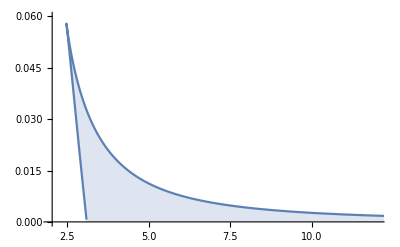

```mathematica
ListLinePlot[{ddEcoRV},PlotRange->{{2,12},{0,0.06}}, Filling->Bottom]
```

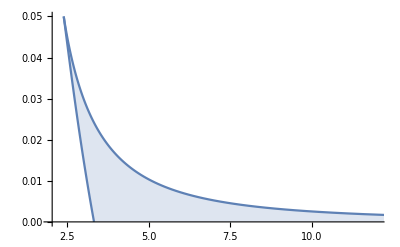

```mathematica
ListLinePlot[{ddEsp1396I},PlotRange->{{2,12},{0,0.05}}, Filling->Bottom]
```

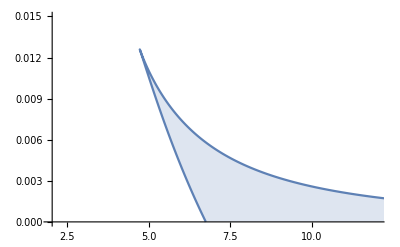

```mathematica
ListLinePlot[{ddAhDI},PlotRange->{{2,12},{0,0.015}}, Filling->Bottom]
```